Jessica Yee
UID: 104938481
jessica23424@g.ucla.edu
HW3

```mathematica
Remove["Global`*"] (*number1*)
SetAttributes[{R, omega}, Constant]
X[t_]:=R*Cos[omega*t]+R*Cos[phi+omega*t]
Y[t_]:=R*Cos[omega*t]+R*Cos[phi+omega*t]
Xd[t_]:=-R*omega*Sin[omega*t]-R*(phid+omega)*Sin[phi+omega*t]
Yd[t_]:=R*omega*Cos[omega*t]-R*(phid+omega)*Cos[phi+omega*t]
L[omega_,phi_,phid_]:=1/2*m*((Xd[t])^2+(Yd[t])^2)+m*g*Y[t]
FullSimplify[Evaluate[L[omega, phi, phid]]]
```

1/2 m R (2 g (Cos[omega t]+Cos[phi+omega t])+R (2 omega^2+2 omega phid+phid^2-2 omega (omega+phid) Cos[phi+2 omega t]))

```mathematica
Remove["Global`*"] (*number 2*)
Assuming[Element[beta, Reals],Simplify[DSolve[{X''[t]+2*beta*X'[t]+omega^2*X[t]==0, X'[0]==0, X[0]==1}, X,t]]]
Assuming[Element[b, Reals],Simplify[DSolve[{X''[t]+b/m*X'[t]+Sqrt[k/m]^2*X[t]==0, X'[0]==0, X[0]==1}, X,t]]]
```

{{X→Function[{t},(-beta ⅇ^((-beta-√(beta^2-omega^2)) t)+beta ⅇ^((-beta+√(beta^2-omega^2)) t)+ⅇ^((-beta-√(beta^2-omega^2)) t) √(beta^2-omega^2)+ⅇ^((-beta+√(beta^2-omega^2)) t) √(beta^2-omega^2))/(2 √(beta^2-omega^2))]}}

{{X→Function[{t},(-b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t)+b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t)+ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) √(b^2-4 k m)+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) √(b^2-4 k m))/(2 √(b^2-4 k m))]}}

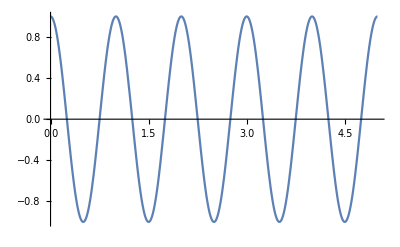

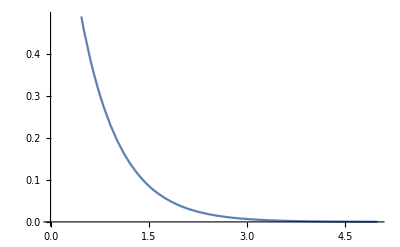

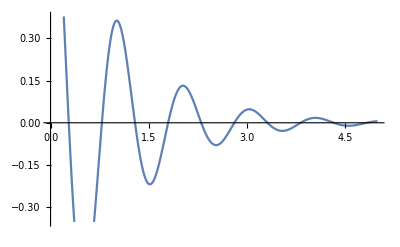

```mathematica
X[t_]:=(-beta ⅇ^((-beta-√(beta^2-omega^2)) t)+beta ⅇ^((-beta+√(beta^2-omega^2)) t)+ⅇ^((-beta-√(beta^2-omega^2)) t) √(beta^2-omega^2)+ⅇ^((-beta+√(beta^2-omega^2)) t) √(beta^2-omega^2))/(2 √(beta^2-omega^2))
X2[t_]:=(-b ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t)+b ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t)+ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) √(b^2-4 k m)+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) √(b^2-4 k m))/(2 √(b^2-4 k m))
omega=2*Pi; beta=0;
Plot[X[t], {t,0,5}]
beta=4*Pi;
Plot[X[t],{t,0,5}]
Clear[beta];
Clear[omega];
b=2*m;
k=omega^2*m;
m=1;
omega=2Pi;
Simplify[X2[t]];

Plot[X2[t],{t,0,5}]
```

```mathematica
(*number 3*)
Remove["Global`*"]

DSolve[{x''[t]+beta*x'[t]+2^2*x[t]==0, x[0]==1, x'[0]==0}, x,t]
```

{{x→Function[{t},(-beta ⅇ^(1/2 (-beta-√(-16+beta^2)) t)+√(-16+beta^2) ⅇ^(1/2 (-beta-√(-16+beta^2)) t)+beta ⅇ^(1/2 (-beta+√(-16+beta^2)) t)+√(-16+beta^2) ⅇ^(1/2 (-beta+√(-16+beta^2)) t))/(2 √(-16+beta^2))]}}

```mathematica
X[t_, beta_]:=(-beta ⅇ^(1/2 (-beta-√(-16+beta^2)) t)+√(-16+beta^2) ⅇ^(1/2 (-beta-√(-16+beta^2)) t)+beta ⅇ^(1/2 (-beta+√(-16+beta^2)) t)+√(-16+beta^2) ⅇ^(1/2 (-beta+√(-16+beta^2)) t))/(2 √(-16+beta^2))
Manipulate[Plot[X[t, beta],{t,0,5}], {beta,0,3.99,0.1}]
```

```mathematica
Remove["Global`*"] (*number 4*)

FullSimplify[Assuming[{k>0, m>0, Element[k,Reals], Element[m, Reals] },DSolve[{x2''[t]+Pi*x2'[t]+(2Pi)^2*x2[t]==Sin[2Pi*t], x2[0]==0, x2'[0]==0}, x2,t]]]
```

{{x2→Function[{t},1/(60 π^2)ⅇ^(-(π t)/2) (30 Cos[1/2 √15 π t]-15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Cos[1/2 (-4+√15) π t]-4 √15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Cos[1/2 (-4+√15) π t]-15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Cos[1/2 (4+√15) π t]+4 √15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Cos[1/2 (4+√15) π t]+2 √15 Sin[1/2 √15 π t]-√15 ⅇ^((π t)/2) Cos[1/2 (-4+√15) π t] Sin[1/2 √15 π t]-√15 ⅇ^((π t)/2) Cos[1/2 (4+√15) π t] Sin[1/2 √15 π t]+8 √15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Sin[2 π t] Sin[1/2 √15 π t]-30 ⅇ^((π t)/2) Cos[π t]^2 Sin[1/2 √15 π t]^2+30 ⅇ^((π t)/2) Sin[π t]^2 Sin[1/2 √15 π t]^2+√15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Sin[1/2 (-4+√15) π t]+√15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Sin[1/2 (4+√15) π t])]}}

```mathematica
X2[t_]:=1/(60 π^2)ⅇ^(-(π t)/2) (30 Cos[1/2 √15 π t]-15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Cos[1/2 (-4+√15) π t]-4 √15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Cos[1/2 (-4+√15) π t]-15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Cos[1/2 (4+√15) π t]+4 √15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Cos[1/2 (4+√15) π t]+2 √15 Sin[1/2 √15 π t]-√15 ⅇ^((π t)/2) Cos[1/2 (-4+√15) π t] Sin[1/2 √15 π t]-√15 ⅇ^((π t)/2) Cos[1/2 (4+√15) π t] Sin[1/2 √15 π t]+8 √15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Sin[2 π t] Sin[1/2 √15 π t]-30 ⅇ^((π t)/2) Cos[π t]^2 Sin[1/2 √15 π t]^2+30 ⅇ^((π t)/2) Sin[π t]^2 Sin[1/2 √15 π t]^2+√15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Sin[1/2 (-4+√15) π t]+√15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Sin[1/2 (4+√15) π t])
FullSimplify[DSolve[{x1''[t]+Pi*x1'[t]+(2Pi)^2*x1[t]==0, x1[1/2]==X2[1/2],x1'[1/2]==X2'[1/2]}, x1,t]]
```

{{x1→Function[{t},1/(60 π^2 (Cos[(√15 π)/4]^2+Sin[(√15 π)/4]^2))ⅇ^(-(π t)/2) (30 Cos[(√15 π)/4]^2 Cos[1/2 √15 π t]-15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (-4+√15) π] Cos[1/2 √15 π t]-4 √15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (-4+√15) π] Cos[1/2 √15 π t]-15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (4+√15) π] Cos[1/2 √15 π t]+4 √15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (4+√15) π] Cos[1/2 √15 π t]+8 ⅇ^(π/4) Cos[(√15 π)/4] Cos[1/4 (-4+√15) π] Cos[1/2 √15 π t] Sin[(√15 π)/4]-8 ⅇ^(π/4) Cos[(√15 π)/4] Cos[1/4 (4+√15) π] Cos[1/2 √15 π t] Sin[(√15 π)/4]+30 Cos[1/2 √15 π t] Sin[(√15 π)/4]^2+2 ⅇ^(π/4) Cos[(√15 π)/4] Cos[1/2 √15 π t] Sin[(√15 π)/4]^2-14 ⅇ^(π/4) Cos[1/4 (-4+√15) π] Cos[1/2 √15 π t] Sin[(√15 π)/4]^2-4 √15 ⅇ^(π/4) Cos[1/4 (-4+√15) π] Cos[1/2 √15 π t] Sin[(√15 π)/4]^2-14 ⅇ^(π/4) Cos[1/4 (4+√15) π] Cos[1/2 √15 π t] Sin[(√15 π)/4]^2+4 √15 ⅇ^(π/4) Cos[1/4 (4+√15) π] Cos[1/2 √15 π t] Sin[(√15 π)/4]^2-2 √15 ⅇ^(π/4) Cos[1/2 √15 π t] Sin[(√15 π)/4]^3+√15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/2 √15 π t] Sin[1/4 (-4+√15) π]+4 ⅇ^(π/4) Cos[1/2 √15 π t] Sin[(√15 π)/4]^2 Sin[1/4 (-4+√15) π]+√15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/2 √15 π t] Sin[1/4 (4+√15) π]-4 ⅇ^(π/4) Cos[1/2 √15 π t] Sin[(√15 π)/4]^2 Sin[1/4 (4+√15) π]+2 √15 Cos[(√15 π)/4]^2 Sin[1/2 √15 π t]-8 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (-4+√15) π] Sin[1/2 √15 π t]-√15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (-4+√15) π] Sin[1/2 √15 π t]+8 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (4+√15) π] Sin[1/2 √15 π t]-√15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (4+√15) π] Sin[1/2 √15 π t]+28 ⅇ^(π/4) Cos[(√15 π)/4]^2 Sin[(√15 π)/4] Sin[1/2 √15 π t]-ⅇ^(π/4) Cos[(√15 π)/4] Cos[1/4 (-4+√15) π] Sin[(√15 π)/4] Sin[1/2 √15 π t]-ⅇ^(π/4) Cos[(√15 π)/4] Cos[1/4 (4+√15) π] Sin[(√15 π)/4] Sin[1/2 √15 π t]+2 √15 Sin[(√15 π)/4]^2 Sin[1/2 √15 π t]+2 √15 ⅇ^(π/4) Cos[(√15 π)/4] Sin[(√15 π)/4]^2 Sin[1/2 √15 π t]-√15 ⅇ^(π/4) Cos[1/4 (-4+√15) π] Sin[(√15 π)/4]^2 Sin[1/2 √15 π t]-√15 ⅇ^(π/4) Cos[1/4 (4+√15) π] Sin[(√15 π)/4]^2 Sin[1/2 √15 π t]+30 ⅇ^(π/4) Sin[(√15 π)/4]^3 Sin[1/2 √15 π t]-4 ⅇ^(π/4) Cos[(√15 π)/4] Sin[(√15 π)/4] Sin[1/4 (-4+√15) π] Sin[1/2 √15 π t]+√15 ⅇ^(π/4) Cos[(√15 π)/4] Sin[(√15 π)/4] Sin[1/4 (-4+√15) π] Sin[1/2 √15 π t]+4 ⅇ^(π/4) Cos[(√15 π)/4] Sin[(√15 π)/4] Sin[1/4 (4+√15) π] Sin[1/2 √15 π t]+√15 ⅇ^(π/4) Cos[(√15 π)/4] Sin[(√15 π)/4] Sin[1/4 (4+√15) π] Sin[1/2 √15 π t])]}}

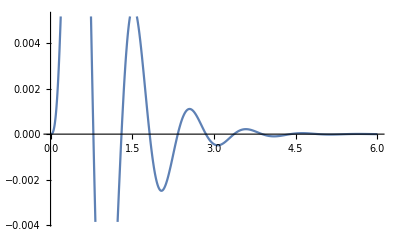

```mathematica
Remove["Global`*"]
X1[t_]:=1/(60 π^2 (Cos[(√15 π)/4]^2+Sin[(√15 π)/4]^2))ⅇ^(-(π t)/2) (30 Cos[(√15 π)/4]^2 Cos[1/2 √15 π t]-15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (-4+√15) π] Cos[1/2 √15 π t]-4 √15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (-4+√15) π] Cos[1/2 √15 π t]-15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (4+√15) π] Cos[1/2 √15 π t]+4 √15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (4+√15) π] Cos[1/2 √15 π t]+8 ⅇ^(π/4) Cos[(√15 π)/4] Cos[1/4 (-4+√15) π] Cos[1/2 √15 π t] Sin[(√15 π)/4]-8 ⅇ^(π/4) Cos[(√15 π)/4] Cos[1/4 (4+√15) π] Cos[1/2 √15 π t] Sin[(√15 π)/4]+30 Cos[1/2 √15 π t] Sin[(√15 π)/4]^2+2 ⅇ^(π/4) Cos[(√15 π)/4] Cos[1/2 √15 π t] Sin[(√15 π)/4]^2-14 ⅇ^(π/4) Cos[1/4 (-4+√15) π] Cos[1/2 √15 π t] Sin[(√15 π)/4]^2-4 √15 ⅇ^(π/4) Cos[1/4 (-4+√15) π] Cos[1/2 √15 π t] Sin[(√15 π)/4]^2-14 ⅇ^(π/4) Cos[1/4 (4+√15) π] Cos[1/2 √15 π t] Sin[(√15 π)/4]^2+4 √15 ⅇ^(π/4) Cos[1/4 (4+√15) π] Cos[1/2 √15 π t] Sin[(√15 π)/4]^2-2 √15 ⅇ^(π/4) Cos[1/2 √15 π t] Sin[(√15 π)/4]^3+√15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/2 √15 π t] Sin[1/4 (-4+√15) π]+4 ⅇ^(π/4) Cos[1/2 √15 π t] Sin[(√15 π)/4]^2 Sin[1/4 (-4+√15) π]+√15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/2 √15 π t] Sin[1/4 (4+√15) π]-4 ⅇ^(π/4) Cos[1/2 √15 π t] Sin[(√15 π)/4]^2 Sin[1/4 (4+√15) π]+2 √15 Cos[(√15 π)/4]^2 Sin[1/2 √15 π t]-8 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (-4+√15) π] Sin[1/2 √15 π t]-√15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (-4+√15) π] Sin[1/2 √15 π t]+8 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (4+√15) π] Sin[1/2 √15 π t]-√15 ⅇ^(π/4) Cos[(√15 π)/4]^2 Cos[1/4 (4+√15) π] Sin[1/2 √15 π t]+28 ⅇ^(π/4) Cos[(√15 π)/4]^2 Sin[(√15 π)/4] Sin[1/2 √15 π t]-ⅇ^(π/4) Cos[(√15 π)/4] Cos[1/4 (-4+√15) π] Sin[(√15 π)/4] Sin[1/2 √15 π t]-ⅇ^(π/4) Cos[(√15 π)/4] Cos[1/4 (4+√15) π] Sin[(√15 π)/4] Sin[1/2 √15 π t]+2 √15 Sin[(√15 π)/4]^2 Sin[1/2 √15 π t]+2 √15 ⅇ^(π/4) Cos[(√15 π)/4] Sin[(√15 π)/4]^2 Sin[1/2 √15 π t]-√15 ⅇ^(π/4) Cos[1/4 (-4+√15) π] Sin[(√15 π)/4]^2 Sin[1/2 √15 π t]-√15 ⅇ^(π/4) Cos[1/4 (4+√15) π] Sin[(√15 π)/4]^2 Sin[1/2 √15 π t]+30 ⅇ^(π/4) Sin[(√15 π)/4]^3 Sin[1/2 √15 π t]-4 ⅇ^(π/4) Cos[(√15 π)/4] Sin[(√15 π)/4] Sin[1/4 (-4+√15) π] Sin[1/2 √15 π t]+√15 ⅇ^(π/4) Cos[(√15 π)/4] Sin[(√15 π)/4] Sin[1/4 (-4+√15) π] Sin[1/2 √15 π t]+4 ⅇ^(π/4) Cos[(√15 π)/4] Sin[(√15 π)/4] Sin[1/4 (4+√15) π] Sin[1/2 √15 π t]+√15 ⅇ^(π/4) Cos[(√15 π)/4] Sin[(√15 π)/4] Sin[1/4 (4+√15) π] Sin[1/2 √15 π t])
X2[t_]:=1/(60 π^2)ⅇ^(-(π t)/2) (30 Cos[1/2 √15 π t]-15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Cos[1/2 (-4+√15) π t]-4 √15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Cos[1/2 (-4+√15) π t]-15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Cos[1/2 (4+√15) π t]+4 √15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Cos[1/2 (4+√15) π t]+2 √15 Sin[1/2 √15 π t]-√15 ⅇ^((π t)/2) Cos[1/2 (-4+√15) π t] Sin[1/2 √15 π t]-√15 ⅇ^((π t)/2) Cos[1/2 (4+√15) π t] Sin[1/2 √15 π t]+8 √15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Sin[2 π t] Sin[1/2 √15 π t]-30 ⅇ^((π t)/2) Cos[π t]^2 Sin[1/2 √15 π t]^2+30 ⅇ^((π t)/2) Sin[π t]^2 Sin[1/2 √15 π t]^2+√15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Sin[1/2 (-4+√15) π t]+√15 ⅇ^((π t)/2) Cos[1/2 √15 π t] Sin[1/2 (4+√15) π t])
Plot[Piecewise[{{X1[t], t>1/2},{X2[t], t>0 && t< 1/2}}],{t,0,6}]
```